{0.49 ⅇ^(-1/2 (12+x)^2),4.84 ⅇ^(-x^2/50),ⅇ^(-1/8 (-9+x)^2),ⅇ^(-1/8 (-15+x)^2)}

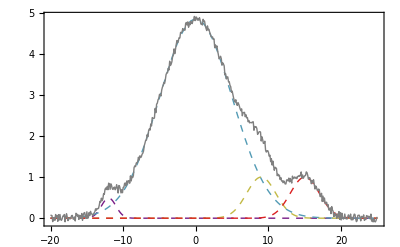

```mathematica
peakfunc[A_,μ_,σ_,x_]:=A^2 E^(-((x-μ)^2/(2 σ^2)));

dataconfig={{.7,-12,1},{2.2,0,5},{1,9,2},{1,15,2}};
datafunc=peakfunc[##,x]&@@@dataconfig
data=Table[{x,Total[datafunc]+.1 RandomReal[{-1,1}]},{x,-20,25,0.1}];

Show@{Plot[datafunc,{x,-20,25},PlotStyle->({Directive[Dashed,Thick,ColorData["Rainbow"][#]]}&/@Rescale[Range[Length[datafunc]]]),PlotRange->All,Frame->True,Axes->False],Graphics[{PointSize[.003],Gray,Line@data}]}
```

```mathematica
Clear[model];
model[data_,n_]:=Module[{dataconfig,modelfunc,objfunc,fitvar,fitres},dataconfig={A[#],μ[#],σ[#]}&/@Range[n];
modelfunc=peakfunc[##,fitvar]&@@@dataconfig//Total;
objfunc=Total[(data[[All,2]]-(modelfunc/.fitvar->#&)/@data[[All,1]])^2];
FindMinimum[objfunc,Flatten@dataconfig]];
```

```mathematica
Clear[modelvalue];
modelvalue[data_,n_]/;NumericQ[n]:=If[n≥1,model[data,n][[1]],0];
```

```mathematica
fitres=ReleaseHold[Hold[{Round[n],model[data,Round[n]]}]/.FindMinimum[modelvalue[data,Round[n]],{n,3},Method->"PrincipalAxis"][[2]]]//Quiet
```

ReplaceAll::reps: {n,3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{Round[n],FindMinimum[objfunc$5232,Flatten[dataconfig$5232]]}/.{n,3}

{1.00852 ⅇ^(-0.128439 (-15.0827+x)^2),1.28833 ⅇ^(-0.0335274 (4.91468+x)^2),0.117636 ⅇ^(-0.61272 (-4.57034+x)^2),0.514394 ⅇ^(-0.516435 (12.0038+x)^2),1.70542 ⅇ^(-0.0853432 (-8.52887+x)^2),2.43862 ⅇ^(-0.0479066 (1.84406+x)^2),2.98503 ⅇ^(-0.0535488 (-2.40782+x)^2),0.116946 ⅇ^(-72.1558 (1.19876+x)^2)}

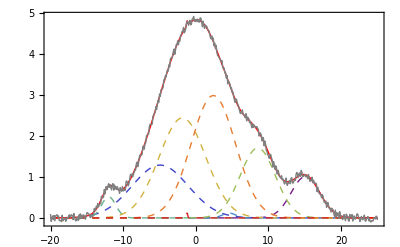

```mathematica
resfunc=peakfunc[A[#],μ[#],σ[#],x]&/@Range[fitres[[1]]]/.fitres[[2,2]]

Show@{Plot[Evaluate[resfunc],{x,-20,25},PlotStyle->({Directive[Dashed,Thick,ColorData["Rainbow"][#]]}&/@Rescale[Range[Length[resfunc]]]),PlotRange->All,Frame->True,Axes->False],Plot[Evaluate[Total@resfunc],{x,-20,25},PlotStyle->Directive[Thick,Red],PlotRange->All,Frame->True,Axes->False],Graphics[{PointSize[.003],Gray,Line@data}]}
```

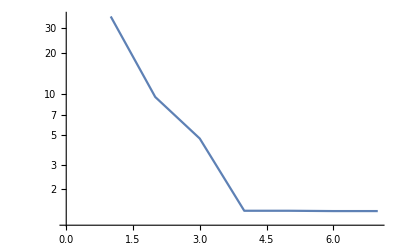

```mathematica
{#,modelvalue[data,#]}&/@Range[1,7]//ListLogPlot[#,Joined->True]&//Quiet
```

FindMinimum::eqineq: Constraints in {(24.0469-ⅇ^(-Plus[«1»]^2/(2 σ[«1»]^2)) A[1]^2-ⅇ^(-(«1»)^2/(2 («1»)^2)) A[2]^2-ⅇ^(-(«1»)^2/(2 («1»)^2)) A[3]^2-ⅇ^(-Plus[«2»]^2/(2 σ[«1»]^2)) A[4]^2)^2} are not all equality or inequality constraints. With the exception of integer domain constraints for linear programming, domain constraints or constraints with Unequal (!=) are not supported.

ReplaceAll::reps: {A[1],μ[1],σ[1],A[2],μ[2],σ[2],A[3],μ[3],σ[3],A[4],μ[4],σ[4]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{ⅇ^(-(x-μ[1])^2/(2 σ[1]^2)) A[1]^2,ⅇ^(-(x-μ[2])^2/(2 σ[2]^2)) A[2]^2,ⅇ^(-(x-μ[3])^2/(2 σ[3]^2)) A[3]^2,ⅇ^(-(x-μ[4])^2/(2 σ[4]^2)) A[4]^2}/.{A[1],μ[1],σ[1],A[2],μ[2],σ[2],A[3],μ[3],σ[3],A[4],μ[4],σ[4]}

ReplaceAll::reps: {A[1],μ[1],σ[1],A[2],μ[2],σ[2],A[3],μ[3],σ[3],A[4],μ[4],σ[4]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {A[1.],μ[1.],σ[1.],A[2.],μ[2.],σ[2.],A[3.],μ[3.],σ[3.],A[4.],μ[4.],σ[4.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Total::tllen: Lists of unequal length in {ⅇ^(-(x+Times[«2»])^2/(2 σ[1]^2)) A[1]^2,ⅇ^(-(x+Times[«2»])^2/(2 σ[2]^2)) A[2]^2,ⅇ^(-(x+Times[«2»])^2/(2 σ[3]^2)) A[3]^2,ⅇ^(-(x+Times[«2»])^2/(2 σ[4]^2)) A[4]^2}/.{A[1],μ[1],σ[1],A[2],μ[2],σ[2],A[3],μ[3],σ[3],A[4],μ[4],σ[4]} cannot be added.

Total::tllen: Lists of unequal length in {ⅇ^(-(-19.9991+Times[«1»])^2/(2 σ[1]^2)) A[1]^2,ⅇ^(-(-«19»+Times[«2»])^2/(2 σ[2]^2)) A[2]^2,ⅇ^(-(-«19»+Times[«1»])^2/(2 σ[3]^2)) A[3]^2,ⅇ^(-(-19.9991+«1»)^2/(2 σ[4]^2)) A[4]^2}/.{A[1],μ[1],σ[1],A[2],μ[2],σ[2],A[3],μ[3],σ[3],A[4],μ[4],σ[4]} cannot be added.

Total::tllen: Lists of unequal length in {2.71828^(-(0.5 (-19.9991+«1»)^2)/σ[1.]^2) A[1.]^2,2.71828^(-(0.5 («1»)^2)/σ[2.]^2) A[2.]^2,2.71828^(-(0.5 (-«19»+«1»)^2)/σ[3.]^2) A[3.]^2,2.71828^(-(0.5 (-«19»+Times[«2»])^2)/σ[4.]^2) A[4.]^2}/.{A[1.],μ[1.],σ[1.],A[2.],μ[2.],σ[2.],A[3.],μ[3.],σ[3.],A[4.],μ[4.],σ[4.]} cannot be added.

General::stop: Further output of Total::tllen will be suppressed during this calculation.

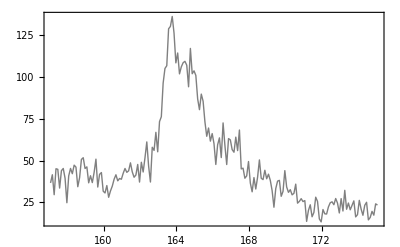

```mathematica
model[data_,n_]:=Module[{dataconfig,modelfunc,objfunc,fitvar,fitres},dataconfig={A[#],μ[#],σ[#]}&/@Range[n];
modelfunc=peakfunc[##,fitvar]&@@@dataconfig//Total;
objfunc=Total[(data[[All,2]]-(modelfunc/.fitvar->#&)/@data[[All,1]])^2];
FindMinimum[objfunc,Flatten@dataconfig]];
modelvalue[data_,n_]/;NumericQ[n]:=If[n≥1,model[data,n][[1]],0];
peakfunc[A_,μ_,σ_,x_]:=A^2 E^(-((x-μ)^2/(2 σ^2)));

With[{n=4},resfunc=peakfunc[A[#],μ[#],σ[#],x]&/@Range[n]/.model[data,n][[2]]]

Show@{Plot[Evaluate[resfunc],{x,-20,25},PlotStyle->({Directive[Dashed,Thick,ColorData["Rainbow"][#]]}&/@Rescale[Range[Length[resfunc]]]),PlotRange->All,Frame->True,Axes->False],Plot[Evaluate[Total@resfunc],{x,-20,25},PlotStyle->Directive[Thick,Red],PlotRange->All,Frame->True,Axes->False],Graphics[{PointSize[.003],Gray,Line@data}]}
```

```mathematica
metadata={{{175.08,23.3185},{174.98,24.04685714285715},{174.88,17.261607142857144},{174.78,19.534000000000006},{174.68,15.86564285714286},{174.58,14.441392857142858},{174.48,24.981571428571442},{174.38,23.17053571428572},{174.28,17.1904642857143},{174.18,20.921821428571434},{174.08,26.13057142857143},{173.98,17.569000000000003},{173.88,16.23003571428572},{173.78,25.826607142857142},{173.68,23.13196428571429},{173.58,20.481035714285724},{173.48,24.53521428571429},{173.38,20.808142857142855},{173.28,32.1424642857143},{173.18,19.7547142857143},{173.08,27.18614285714287},{172.98,18.583000000000013},{172.88,24.501785714285717},{172.78,27.240142857142857},{172.68,23.51992857142858},{172.58,25.258964285714285},{172.48,24.710607142857157},{172.38,22.217071428571444},{172.28,17.953214285714296},{172.18,18.0565},{172.08,20.641428571428577},{171.98,13.233571428571437},{171.88,15.015892857142859},{171.78,25.47807142857144},{171.68,28.036750000000012},{171.58,18.879250000000013},{171.48,16.30257142857144},{171.38,23.486500000000007},{171.28,20.14792857142858},{171.18,13.543107142857153},{171.08,25.989142857142852},{170.98,25.403071428571437},{170.88,27.15357142857144},{170.78,25.512785714285712},{170.68,24.466214285714287},{170.58,35.84853571428572},{170.48,30.331857142857146},{170.38,29.442678571428573},{170.28,32.548},{170.18,30.92264285714286},{170.08,34.163928571428585},{169.98,43.945750000000004},{169.88,31.522857142857134},{169.78,28.56625000000001},{169.68,38.110107142857146},{169.58,37.65432142857142},{169.48,33.164928571428575},{169.38,22.015107142857147},{169.28,31.98207142857143},{169.18,38.08996428571429},{169.08,41.80675000000001},{168.98,39.067535714285725},{168.88,44.159285714285716},{168.78,38.564607142857156},{168.68,39.3595},{168.58,50.35975000000002},{168.48,40.04971428571429},{168.38,32.923214285714295},{168.28,39.776178571428574},{168.18,31.253178571428563},{168.08,36.50789285714288},{167.98,49.399321428571426},{167.88,40.78460714285714},{167.78,39.38650000000001},{167.68,45.415000000000006},{167.58,44.95975},{167.48,68.26284999999999},{167.38,55.9315},{167.28,64.00359999999999},{167.18,54.9658},{167.08,56.512},{166.98,62.346999999999994},{166.88,63.14410000000001},{166.78,47.59660000000001},{166.68,59.08584999999999},{166.58,72.51805000000002},{166.48,51.753249999999994},{166.38,63.56184999999999},{166.28,59.4436},{166.18,47.62480000000001},{166.08,60.06115},{165.98,66.1225},{165.88,61.59610000000001},{165.78,69.46224999999998},{165.68,64.50655},{165.58,73.20895000000002},{165.48,85.53235000000001},{165.38,89.77435},{165.28,80.446},{165.18,86.93574999999998},{165.08,100.96000000000001},{164.98,103.72149999999999},{164.88,101.9785},{164.78,117.13150000000002},{164.68,94.15300000000002},{164.58,107.07849999999999},{164.48,109.40350000000001},{164.38,108.56649999999999},{164.28,106.096},{164.18,101.887},{164.08,114.39699999999999},{163.98,108.47199999999998},{163.88,126.208},{163.78,136.27450000000002},{163.68,130.3195},{163.58,128.8795},{163.48,106.77699999999999},{163.38,105.13150000000002},{163.28,96.35589999999999},{163.18,76.22815},{163.08,73.29055000000001},{162.98,55.21135000000001},{162.88,66.87519999999999},{162.78,56.05645000000001},{162.68,57.9268},{162.58,37.1134},{162.48,46.657899999999984},{162.38,61.1386},{162.28,51.65845},{162.18,43.1164},{162.08,48.948999999999984},{161.98,37.084599999999995},{161.88,47.636799999999994},{161.78,41.3236},{161.68,39.9658},{161.58,43.1836},{161.48,48.606849999999994},{161.38,43.8301},{161.28,42.91839999999999},{161.18,45.2239},{161.08,42.33970000000001},{160.98,38.778549999999996},{160.88,39.234700000000004},{160.78,37.8193},{160.68,41.46039999999999},{160.58,38.784549999999996},{160.48,34.6669},{160.38,31.756299999999996},{160.28,27.97120000000001},{160.18,34.99584999999999},{160.08,30.55945},{159.98,31.613500000000002},{159.88,42.77544999999999},{159.78,41.72155000000001},{159.68,34.1074},{159.58,50.81815},{159.48,42.88239999999999},{159.38,36.77485},{159.28,40.8745},{159.18,36.63145},{159.08,46.19874999999999},{158.98,45.217299999999994},{158.88,51.68185},{158.78,50.65899999999999},{158.68,39.75085},{158.58,34.299549999999996},{158.48,46.03240000000001},{158.38,47.230450000000005},{158.28,42.0925},{158.18,45.249700000000004},{158.08,40.761700000000005},{157.98,24.70765},{157.88,39.3775},{157.78,45.21969999999999},{157.68,43.94725},{157.58,33.489850000000004},{157.48,44.723349999999996},{157.38,45.072100000000006},{157.28,29.516800000000003},{157.18,41.467600000000004},{157.08,36.57745}}};
```

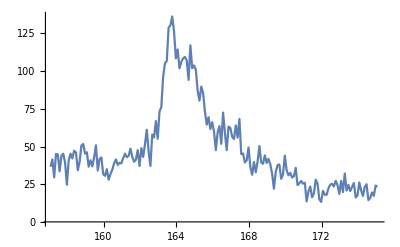

```mathematica
ListLinePlot[data]
```

```mathematica
data={{{175.08,70.7983},{174.98,66.7747},{174.88,70.4482},{174.78,69.8379},{174.68,68.0759},{174.58,65.9604},{174.48,62.7998},{174.38,60.0687},{174.28,67.3389},{174.18,58.5981},{174.08,71.4706},{173.98,57.9872},{173.88,57.9352},{173.78,55.0594},{173.68,66.3752},{173.58,61.9968},{173.48,54.5985},{173.38,58.5081},{173.28,68.0092},{173.18,61.2585},{173.08,60.7643},{172.98,55.907},{172.88,58.9442},{172.78,67.3316},{172.68,62.0775},{172.58,54.91},{172.48,58.1313},{172.38,60.3221},{172.28,54.8379},{172.18,55.2988},{172.08,55.1274},{171.98,68.5528},{171.88,60.0687},{171.78,67.2035},{171.68,56.2718},{171.58,54.8466},{171.48,64.6839},{171.38,60.4468},{171.28,61.9941},{171.18,67.1549},{171.08,61.0404},{170.98,62.1682},{170.88,63.2126},{170.78,64.3104},{170.68,68.9062},{170.58,74.2584},{170.48,76.9154},{170.38,74.7459},{170.28,86.4266},{170.18,85.2388},{170.08,91.4819},{169.98,93.6261},{169.88,84.0336},{169.78,97.3016},{169.68,101.259},{169.58,107.168},{169.48,97.9298},{169.38,98.8122},{169.28,93.8742},{169.18,107.936},{169.08,111.173},{168.98,99.4118},{168.88,117.878},{168.78,116.787},{168.68,116.323},{168.58,105.62},{168.48,93.5407},{168.38,100.712},{168.28,102.011},{168.18,105.956},{168.08,100.932},{167.98,94.4564},{167.88,81.2178},{167.78,73.1586},{167.68,72.1115},{167.58,74.233},{167.48,71.4726},{167.38,69.2003},{167.28,81.4432},{167.18,70.3575},{167.08,76.7187},{166.98,63.7722},{166.88,58.8869},{166.78,67.9152},{166.68,70.9744},{166.58,71.3852},{166.48,60.8884},{166.38,63.32},{166.28,54.8579},{166.18,65.737},{166.08,75.815},{165.98,62.8845},{165.88,73.0686},{165.78,66.3252},{165.68,60.1881},{165.58,68.9009},{165.48,65.2814},{165.38,62.7358},{165.28,78.2146},{165.18,86.6993},{165.08,91.1658},{164.98,84.3938},{164.88,82.2809},{164.78,89.8966},{164.68,81.2852},{164.58,83.1913},{164.48,87.1535},{164.38,95.9097},{164.28,93.6295},{164.18,84.6912},{164.08,97.7558},{163.98,99.145},{163.88,92.473},{163.78,108.9},{163.68,97.5257},{163.58,92.7051},{163.48,90.5649},{163.38,88.2493},{163.28,94.0656},{163.18,79.083},{163.08,82.2342},{162.98,75.803},{162.88,70.0874},{162.78,54.5385},{162.68,77.5797},{162.58,57.4436},{162.48,57.3116},{162.38,64.3297},{162.28,66.7827},{162.18,66.0878},{162.08,62.1622},{161.98,62.3376},{161.88,61.1898},{161.78,52.1515},{161.68,53.5174},{161.58,56.3559},{161.48,55.01},{161.38,48.4314},{161.28,58.6255},{161.18,58.0232},{161.08,59.964},{160.98,52.1148},{160.88,59.6559},{160.78,55.749},{160.68,49.9226},{160.58,56.8874},{160.48,52.7238},{160.38,47.8531},{160.28,52.0975},{160.18,57.6717},{160.08,58.9509},{159.98,56.9881},{159.88,71.1458},{159.78,47.7691},{159.68,60.0514},{159.58,57.3616},{159.48,48.1379},{159.38,43.0486},{159.28,59.1537},{159.18,55.6149},{159.08,47.8025},{158.98,49.4638},{158.88,57.8591},{158.78,48.6801},{158.68,49.928},{158.58,57.7151},{158.48,62.4937},{158.38,45.9197},{158.28,54.7973},{158.18,64.139},{158.08,58.6981},{157.98,55.6056},{157.88,56.708},{157.78,51.9461},{157.68,58.248},{157.58,56.9615},{157.48,56.0171},{157.38,64.9133},{157.28,54.4538},{157.18,53.4887},{157.08,54.4985}},{{175.08,23.3185},{174.98,24.04685714285715},{174.88,17.261607142857144},{174.78,19.534000000000006},{174.68,15.86564285714286},{174.58,14.441392857142858},{174.48,24.981571428571442},{174.38,23.17053571428572},{174.28,17.1904642857143},{174.18,20.921821428571434},{174.08,26.13057142857143},{173.98,17.569000000000003},{173.88,16.23003571428572},{173.78,25.826607142857142},{173.68,23.13196428571429},{173.58,20.481035714285724},{173.48,24.53521428571429},{173.38,20.808142857142855},{173.28,32.1424642857143},{173.18,19.7547142857143},{173.08,27.18614285714287},{172.98,18.583000000000013},{172.88,24.501785714285717},{172.78,27.240142857142857},{172.68,23.51992857142858},{172.58,25.258964285714285},{172.48,24.710607142857157},{172.38,22.217071428571444},{172.28,17.953214285714296},{172.18,18.0565},{172.08,20.641428571428577},{171.98,13.233571428571437},{171.88,15.015892857142859},{171.78,25.47807142857144},{171.68,28.036750000000012},{171.58,18.879250000000013},{171.48,16.30257142857144},{171.38,23.486500000000007},{171.28,20.14792857142858},{171.18,13.543107142857153},{171.08,25.989142857142852},{170.98,25.403071428571437},{170.88,27.15357142857144},{170.78,25.512785714285712},{170.68,24.466214285714287},{170.58,35.84853571428572},{170.48,30.331857142857146},{170.38,29.442678571428573},{170.28,32.548},{170.18,30.92264285714286},{170.08,34.163928571428585},{169.98,43.945750000000004},{169.88,31.522857142857134},{169.78,28.56625000000001},{169.68,38.110107142857146},{169.58,37.65432142857142},{169.48,33.164928571428575},{169.38,22.015107142857147},{169.28,31.98207142857143},{169.18,38.08996428571429},{169.08,41.80675000000001},{168.98,39.067535714285725},{168.88,44.159285714285716},{168.78,38.564607142857156},{168.68,39.3595},{168.58,50.35975000000002},{168.48,40.04971428571429},{168.38,32.923214285714295},{168.28,39.776178571428574},{168.18,31.253178571428563},{168.08,36.50789285714288},{167.98,49.399321428571426},{167.88,40.78460714285714},{167.78,39.38650000000001},{167.68,45.415000000000006},{167.58,44.95975},{167.48,68.26284999999999},{167.38,55.9315},{167.28,64.00359999999999},{167.18,54.9658},{167.08,56.512},{166.98,62.346999999999994},{166.88,63.14410000000001},{166.78,47.59660000000001},{166.68,59.08584999999999},{166.58,72.51805000000002},{166.48,51.753249999999994},{166.38,63.56184999999999},{166.28,59.4436},{166.18,47.62480000000001},{166.08,60.06115},{165.98,66.1225},{165.88,61.59610000000001},{165.78,69.46224999999998},{165.68,64.50655},{165.58,73.20895000000002},{165.48,85.53235000000001},{165.38,89.77435},{165.28,80.446},{165.18,86.93574999999998},{165.08,100.96000000000001},{164.98,103.72149999999999},{164.88,101.9785},{164.78,117.13150000000002},{164.68,94.15300000000002},{164.58,107.07849999999999},{164.48,109.40350000000001},{164.38,108.56649999999999},{164.28,106.096},{164.18,101.887},{164.08,114.39699999999999},{163.98,108.47199999999998},{163.88,126.208},{163.78,136.27450000000002},{163.68,130.3195},{163.58,128.8795},{163.48,106.77699999999999},{163.38,105.13150000000002},{163.28,96.35589999999999},{163.18,76.22815},{163.08,73.29055000000001},{162.98,55.21135000000001},{162.88,66.87519999999999},{162.78,56.05645000000001},{162.68,57.9268},{162.58,37.1134},{162.48,46.657899999999984},{162.38,61.1386},{162.28,51.65845},{162.18,43.1164},{162.08,48.948999999999984},{161.98,37.084599999999995},{161.88,47.636799999999994},{161.78,41.3236},{161.68,39.9658},{161.58,43.1836},{161.48,48.606849999999994},{161.38,43.8301},{161.28,42.91839999999999},{161.18,45.2239},{161.08,42.33970000000001},{160.98,38.778549999999996},{160.88,39.234700000000004},{160.78,37.8193},{160.68,41.46039999999999},{160.58,38.784549999999996},{160.48,34.6669},{160.38,31.756299999999996},{160.28,27.97120000000001},{160.18,34.99584999999999},{160.08,30.55945},{159.98,31.613500000000002},{159.88,42.77544999999999},{159.78,41.72155000000001},{159.68,34.1074},{159.58,50.81815},{159.48,42.88239999999999},{159.38,36.77485},{159.28,40.8745},{159.18,36.63145},{159.08,46.19874999999999},{158.98,45.217299999999994},{158.88,51.68185},{158.78,50.65899999999999},{158.68,39.75085},{158.58,34.299549999999996},{158.48,46.03240000000001},{158.38,47.230450000000005},{158.28,42.0925},{158.18,45.249700000000004},{158.08,40.761700000000005},{157.98,24.70765},{157.88,39.3775},{157.78,45.21969999999999},{157.68,43.94725},{157.58,33.489850000000004},{157.48,44.723349999999996},{157.38,45.072100000000006},{157.28,29.516800000000003},{157.18,41.467600000000004},{157.08,36.57745}}};
```

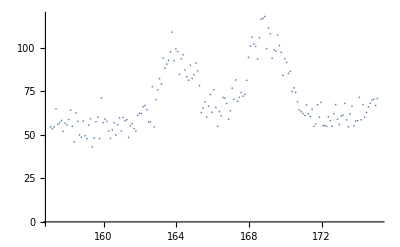

```mathematica
ListPlot[data[[1]],PlotStyle->PointSize[0.003]]
```

```mathematica
EstimatedBackground[data[[1]][[2]]]
```

{69.7737,66.7747}

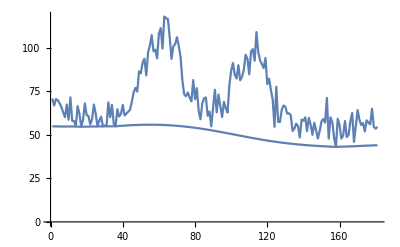

```mathematica
Show@@(({ListLinePlot@#,ListLinePlot@@{(#~EstimatedBackground~20)},PlotStyle->Red})&@(Last/@data[[1]]))
```

```mathematica
PeakFunction[A_,σ_,x_,μ_]:=A^2 E^(-((x-μ)^2/(2 σ^2)));
```

```mathematica
datafit=EstimatedBackground[(Last/@data[[1]]),20]
```

{54.8303,54.8135,54.7968,54.78,54.7629,54.7458,54.7288,54.7117,54.7316,54.7514,54.7635,54.7588,54.7354,54.701,54.6667,54.6325,54.5985,54.6305,54.6626,54.6578,54.6838,54.7099,54.7175,54.7374,54.7574,54.7775,54.7963,54.8152,54.8341,54.8408,54.8439,54.8468,54.8498,54.866,54.8563,54.8466,54.9363,55.0267,55.1054,55.1757,55.2464,55.3177,55.3894,55.448,55.4953,55.536,55.5768,55.6178,55.6558,55.6939,55.7159,55.7329,55.7411,55.7493,55.7575,55.7534,55.7493,55.7364,55.7179,55.6915,55.6635,55.6321,55.5905,55.54,55.4862,55.4299,55.3633,55.2967,55.2193,55.1424,55.0468,54.9522,54.8544,54.7576,54.6401,54.5241,54.4029,54.2833,54.1432,54.0052,53.864,53.725,53.5673,53.4124,53.2472,53.0851,52.9139,52.7462,52.5634,52.3846,52.1989,52.0176,51.8267,51.6405,51.4442,51.2531,51.0525,50.8575,50.6578,50.4639,50.258,50.0588,49.8544,49.6569,49.4576,49.2653,49.0617,48.8658,48.6664,48.4748,48.2816,48.0961,47.9028,47.7179,47.5398,47.3694,47.1819,47.0033,46.8325,46.6697,46.5072,46.3526,46.1976,46.0503,45.9054,45.7651,45.6256,45.4864,45.3549,45.2306,45.1112,44.9929,44.879,44.7667,44.6572,44.5542,44.4547,44.3585,44.2646,44.1754,44.0916,44.0121,43.932,43.8524,43.7758,43.7044,43.6365,43.5732,43.5114,43.4493,43.3917,43.3345,43.2795,43.2287,43.1781,43.1315,43.0884,43.0486,43.084,43.122,43.1628,43.188,43.2107,43.2476,43.2866,43.328,43.372,43.4148,43.459,43.5031,43.5475,43.5941,43.6388,43.6857,43.735,43.7808,43.8256,43.8723,43.9209,43.9654,44.0116}

```mathematica
Show@@{ListLinePlot@(Last/@data[[1]]),ListLinePlot@datafit}
```

-Graphics-

```mathematica
Transpose[{First/@data[[1]],datafit}]
```

{{175.08,54.8303},{174.98,54.8135},{174.88,54.7968},{174.78,54.78},{174.68,54.7629},{174.58,54.7458},{174.48,54.7288},{174.38,54.7117},{174.28,54.7316},{174.18,54.7514},{174.08,54.7635},{173.98,54.7588},{173.88,54.7354},{173.78,54.701},{173.68,54.6667},{173.58,54.6325},{173.48,54.5985},{173.38,54.6305},{173.28,54.6626},{173.18,54.6578},{173.08,54.6838},{172.98,54.7099},{172.88,54.7175},{172.78,54.7374},{172.68,54.7574},{172.58,54.7775},{172.48,54.7963},{172.38,54.8152},{172.28,54.8341},{172.18,54.8408},{172.08,54.8439},{171.98,54.8468},{171.88,54.8498},{171.78,54.866},{171.68,54.8563},{171.58,54.8466},{171.48,54.9363},{171.38,55.0267},{171.28,55.1054},{171.18,55.1757},{171.08,55.2464},{170.98,55.3177},{170.88,55.3894},{170.78,55.448},{170.68,55.4953},{170.58,55.536},{170.48,55.5768},{170.38,55.6178},{170.28,55.6558},{170.18,55.6939},{170.08,55.7159},{169.98,55.7329},{169.88,55.7411},{169.78,55.7493},{169.68,55.7575},{169.58,55.7534},{169.48,55.7493},{169.38,55.7364},{169.28,55.7179},{169.18,55.6915},{169.08,55.6635},{168.98,55.6321},{168.88,55.5905},{168.78,55.54},{168.68,55.4862},{168.58,55.4299},{168.48,55.3633},{168.38,55.2967},{168.28,55.2193},{168.18,55.1424},{168.08,55.0468},{167.98,54.9522},{167.88,54.8544},{167.78,54.7576},{167.68,54.6401},{167.58,54.5241},{167.48,54.4029},{167.38,54.2833},{167.28,54.1432},{167.18,54.0052},{167.08,53.864},{166.98,53.725},{166.88,53.5673},{166.78,53.4124},{166.68,53.2472},{166.58,53.0851},{166.48,52.9139},{166.38,52.7462},{166.28,52.5634},{166.18,52.3846},{166.08,52.1989},{165.98,52.0176},{165.88,51.8267},{165.78,51.6405},{165.68,51.4442},{165.58,51.2531},{165.48,51.0525},{165.38,50.8575},{165.28,50.6578},{165.18,50.4639},{165.08,50.258},{164.98,50.0588},{164.88,49.8544},{164.78,49.6569},{164.68,49.4576},{164.58,49.2653},{164.48,49.0617},{164.38,48.8658},{164.28,48.6664},{164.18,48.4748},{164.08,48.2816},{163.98,48.0961},{163.88,47.9028},{163.78,47.7179},{163.68,47.5398},{163.58,47.3694},{163.48,47.1819},{163.38,47.0033},{163.28,46.8325},{163.18,46.6697},{163.08,46.5072},{162.98,46.3526},{162.88,46.1976},{162.78,46.0503},{162.68,45.9054},{162.58,45.7651},{162.48,45.6256},{162.38,45.4864},{162.28,45.3549},{162.18,45.2306},{162.08,45.1112},{161.98,44.9929},{161.88,44.879},{161.78,44.7667},{161.68,44.6572},{161.58,44.5542},{161.48,44.4547},{161.38,44.3585},{161.28,44.2646},{161.18,44.1754},{161.08,44.0916},{160.98,44.0121},{160.88,43.932},{160.78,43.8524},{160.68,43.7758},{160.58,43.7044},{160.48,43.6365},{160.38,43.5732},{160.28,43.5114},{160.18,43.4493},{160.08,43.3917},{159.98,43.3345},{159.88,43.2795},{159.78,43.2287},{159.68,43.1781},{159.58,43.1315},{159.48,43.0884},{159.38,43.0486},{159.28,43.084},{159.18,43.122},{159.08,43.1628},{158.98,43.188},{158.88,43.2107},{158.78,43.2476},{158.68,43.2866},{158.58,43.328},{158.48,43.372},{158.38,43.4148},{158.28,43.459},{158.18,43.5031},{158.08,43.5475},{157.98,43.5941},{157.88,43.6388},{157.78,43.6857},{157.68,43.735},{157.58,43.7808},{157.48,43.8256},{157.38,43.8723},{157.28,43.9209},{157.18,43.9654},{157.08,44.0116}}

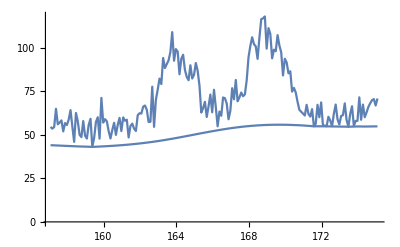

```mathematica
Show@@{ListLinePlot@data[[1]],ListLinePlot@%%}
```

```mathematica
fitteddata=Transpose[{First/@data[[1]],(Last/@#-datafit)&@data[[1]]}]
```

{{175.08,15.968},{174.98,11.9612},{174.88,15.6514},{174.78,15.0579},{174.68,13.313},{174.58,11.2146},{174.48,8.07103},{174.38,5.35696},{174.28,12.6073},{174.18,3.84669},{174.08,16.7071},{173.98,3.22836},{173.88,3.19981},{173.78,0.35841},{173.68,11.7085},{173.58,7.36426},{173.48,0.},{173.38,3.87762},{173.28,13.3466},{173.18,6.60069},{173.08,6.08049},{172.98,1.19712},{172.88,4.22673},{172.78,12.5942},{172.68,7.32007},{172.58,0.132539},{172.48,3.33497},{172.38,5.50691},{172.28,0.00380945},{172.18,0.457967},{172.08,0.283546},{171.98,13.706},{171.88,5.21889},{171.78,12.3375},{171.68,1.41552},{171.58,0.},{171.48,9.74765},{171.38,5.42008},{171.28,6.88871},{171.18,11.9792},{171.08,5.79396},{170.98,6.8505},{170.88,7.82315},{170.78,8.86236},{170.68,13.4109},{170.58,18.7224},{170.48,21.3386},{170.38,19.1281},{170.28,30.7708},{170.18,29.5449},{170.08,35.766},{169.98,37.8932},{169.88,28.2925},{169.78,41.5523},{169.68,45.5015},{169.58,51.4146},{169.48,42.1805},{169.38,43.0758},{169.28,38.1563},{169.18,52.2445},{169.08,55.5095},{168.98,43.7797},{168.88,62.2875},{168.78,61.247},{168.68,60.8368},{168.58,50.1901},{168.48,38.1774},{168.38,45.4153},{168.28,46.7917},{168.18,50.8136},{168.08,45.8852},{167.98,39.5042},{167.88,26.3634},{167.78,18.401},{167.68,17.4714},{167.58,19.7089},{167.48,17.0697},{167.38,14.917},{167.28,27.3},{167.18,16.3523},{167.08,22.8547},{166.98,10.0472},{166.88,5.31959},{166.78,14.5028},{166.68,17.7272},{166.58,18.3001},{166.48,7.97449},{166.38,10.5738},{166.28,2.29455},{166.18,13.3524},{166.08,23.6161},{165.98,10.8669},{165.88,21.2419},{165.78,14.6847},{165.68,8.74391},{165.58,17.6478},{165.48,14.2289},{165.38,11.8783},{165.28,27.5568},{165.18,36.2354},{165.08,40.9078},{164.98,34.335},{164.88,32.4265},{164.78,40.2397},{164.68,31.8276},{164.58,33.926},{164.48,38.0918},{164.38,47.0439},{164.28,44.9631},{164.18,36.2164},{164.08,49.4742},{163.98,51.0489},{163.88,44.5702},{163.78,61.1821},{163.68,49.9859},{163.58,45.3357},{163.48,43.383},{163.38,41.246},{163.28,47.2331},{163.18,32.4133},{163.08,35.727},{162.98,29.4504},{162.88,23.8898},{162.78,8.48823},{162.68,31.6743},{162.58,11.6785},{162.48,11.686},{162.38,18.8433},{162.28,21.4278},{162.18,20.8572},{162.08,17.051},{161.98,17.3447},{161.88,16.3108},{161.78,7.38483},{161.68,8.86019},{161.58,11.8017},{161.48,10.5553},{161.38,4.07285},{161.28,14.3609},{161.18,13.8478},{161.08,15.8724},{160.98,8.10273},{160.88,15.7239},{160.78,11.8966},{160.68,6.14682},{160.58,13.183},{160.48,9.08731},{160.38,4.27995},{160.28,8.58606},{160.18,14.2224},{160.08,15.5592},{159.98,13.6536},{159.88,27.8663},{159.78,4.54038},{159.68,16.8733},{159.58,14.2301},{159.48,5.04947},{159.38,0.},{159.28,16.0697},{159.18,12.4929},{159.08,4.63969},{158.98,6.27579},{158.88,14.6484},{158.78,5.43255},{158.68,6.6414},{158.58,14.3871},{158.48,19.1217},{158.38,2.5049},{158.28,11.3383},{158.18,20.6359},{158.08,15.1506},{157.98,12.0115},{157.88,13.0692},{157.78,8.26036},{157.68,14.513},{157.58,13.1807},{157.48,12.1915},{157.38,21.041},{157.28,10.5329},{157.18,9.52326},{157.08,10.4869}}

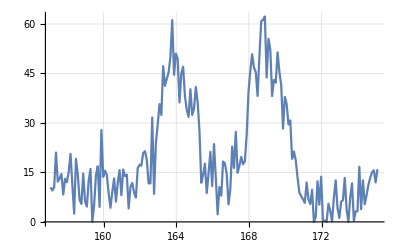

```mathematica
ListLinePlot[fitteddata,ImageSize->Full,GridLines->Automatic]
```

```mathematica
PeakFunction[1,1,1,x]
```

ⅇ^(-1/2 (-1+x)^2)

```mathematica
Array[A,10]=Range[10]
```

Set::write: Tag Array in Array[A,10] is Protected.

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Clear[A]
```

```mathematica
test={{1,1},{2,2},{3,3}};
FindFit[test,A[1]x,A[1],x]
```

{A[1]→1.}

```mathematica
dataconfig={A[#],sigma[#],x}&/@Range[2]
```

{{A[1],sigma[1],x},{A[2],sigma[2],x}}

```mathematica
PeakFunction@@@dataconfig
```

{ⅇ^(-(x-u[1])^2/(2 sigma[1]^2)) A[1]^2,ⅇ^(-(x-u[2])^2/(2 sigma[2]^2)) A[2]^2,ⅇ^(-(x-u[3])^2/(2 sigma[3]^2)) A[3]^2,ⅇ^(-(x-u[4])^2/(2 sigma[4]^2)) A[4]^2}

```mathematica
Plus@@%126
```

ⅇ^(-(x-u[1])^2/(2 sigma[1]^2)) A[1]^2+ⅇ^(-(x-u[2])^2/(2 sigma[2]^2)) A[2]^2+ⅇ^(-(x-u[3])^2/(2 sigma[3]^2)) A[3]^2+ⅇ^(-(x-u[4])^2/(2 sigma[4]^2)) A[4]^2

```mathematica
FindFit[fitteddata,Plus@@%126+c,list3,x]
```

{A[1]→1.,u[1]→1.,sigma[1]→1.,A[2]→1.,u[2]→1.,sigma[2]→1.,A[3]→1.,u[3]→1.,sigma[3]→1.,A[4]→1.,u[4]→1.,sigma[4]→1.,c→19.8534}

```mathematica
{#1[[1]],#2[[1]]}&@@@{{{1,2},{3,3}},{{1,2},{2,3}}}
```

{{1,3},{1,2}}

```mathematica
list=Flatten/@Transpose[{dataconfig,{164,169}}]
```

{{A[1],sigma[1],x,164},{A[2],sigma[2],x,169}}

```mathematica
{{A[1],sigma[1],x,164},{A[2],sigma[2],x,165},{A[3],sigma[3],x,168.5},{A[4],sigma[4],x,170}}
```

```mathematica
FindFit[fitteddata,Plus@@PeakFunction@@@list,Flatten[Drop[#,-1]&/@dataconfig],x]
```

{A[1]→6.64043,sigma[1]→1.34116,A[2]→7.29363,sigma[2]→-1.07347}

```mathematica
Plus@@PeakFunction@@@list/.%189
```

53.1971 ⅇ^(-0.433899 (-169+x)^2)+44.0952 ⅇ^(-0.277979 (-164+x)^2)

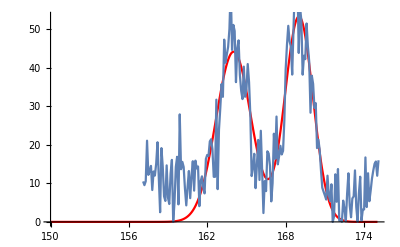

```mathematica
Show[Plot[%,{x,150,175},PlotStyle->Red],ListLinePlot[fitteddata,ImageSize->Full,GridLines->Automatic]]
```

```mathematica
RandomChoice@{Good,Bad}
```

Bad

```mathematica
Select[fitteddata,160<#[[1]]<166&]
```

{{165.98,10.8669},{165.88,21.2419},{165.78,14.6847},{165.68,8.74391},{165.58,17.6478},{165.48,14.2289},{165.38,11.8783},{165.28,27.5568},{165.18,36.2354},{165.08,40.9078},{164.98,34.335},{164.88,32.4265},{164.78,40.2397},{164.68,31.8276},{164.58,33.926},{164.48,38.0918},{164.38,47.0439},{164.28,44.9631},{164.18,36.2164},{164.08,49.4742},{163.98,51.0489},{163.88,44.5702},{163.78,61.1821},{163.68,49.9859},{163.58,45.3357},{163.48,43.383},{163.38,41.246},{163.28,47.2331},{163.18,32.4133},{163.08,35.727},{162.98,29.4504},{162.88,23.8898},{162.78,8.48823},{162.68,31.6743},{162.58,11.6785},{162.48,11.686},{162.38,18.8433},{162.28,21.4278},{162.18,20.8572},{162.08,17.051},{161.98,17.3447},{161.88,16.3108},{161.78,7.38483},{161.68,8.86019},{161.58,11.8017},{161.48,10.5553},{161.38,4.07285},{161.28,14.3609},{161.18,13.8478},{161.08,15.8724},{160.98,8.10273},{160.88,15.7239},{160.78,11.8966},{160.68,6.14682},{160.58,13.183},{160.48,9.08731},{160.38,4.27995},{160.28,8.58606},{160.18,14.2224},{160.08,15.5592}}

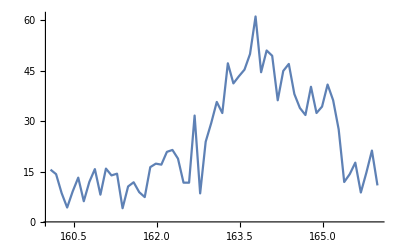

```mathematica
ListLinePlot@%
```

{A[1]→5.76821,sigma[1]→-0.520752,A[2]→5.00841,sigma[2]→-0.582765,c→11.171}

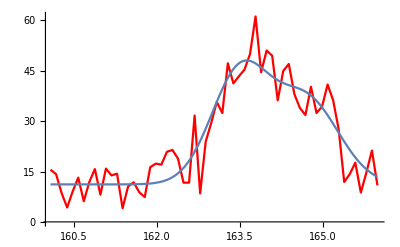

```mathematica
list=Flatten/@Transpose[{dataconfig,{163.5,164.7}}];
FindFit[Select[fitteddata,160<#[[1]]<166&],Plus@@PeakFunction@@@list+c,Append[Flatten[Drop[#,-1]&/@dataconfig],c],x]
Show[ListLinePlot[Select[fitteddata,160<#1⟦1⟧<166&],PlotStyle->Red],Plot[Plus@@Apply[PeakFunction,list,{1}]+c/.%,{x,160.08,165.98}]]
```

```mathematica
PeakFunction[A_,σ_,x_,μ_]:=A^2 E^(-((x-μ)^2/(2 σ^2)));
PeakSplit[data_List,estimatedx_List,BackgroundAdjust_]:=
Module[{xlist,ylist,datafit,fitteddata,background,dataconfig,functionlist,fittedlist,fittedylist,splitylist1,splitylist2,splitline,fittedline,A,sigma},
ylist=Last/@data;
xlist=First/@data;
datafit=EstimatedBackground[ylist,BackgroundAdjust];
fitteddata=Transpose[{xlist,ylist-datafit}];
background=Transpose[{xlist,datafit}];
dataconfig={A[#],sigma[#],x}&/@Range[Length[estimatedx]];
functionlist=PeakFunction@@@(Flatten/@Transpose[{dataconfig,estimatedx}]);
fittedlist=FindFit[fitteddata,Plus@@functionlist,Flatten[Drop[#,-1]&/@dataconfig],x];
fittedylist=((Plus@@functionlist/.fittedlist)/.x->#)&/@xlist+datafit;
splitylist1=((functionlist/.fittedlist)/.x->#)&/@xlist//Transpose;
splitylist2=(#+datafit)&/@splitylist1;
splitline=(Transpose[{xlist,#}])&/@splitylist2;
fittedline=Transpose[{xlist,fittedylist}];
Column[{functionlist/.fittedlist,
Show[ListLinePlot[data,PlotRange->All,PlotStyle->Black],
ListLinePlot[Join[{background},splitline],PlotRange->All,PlotStyle->({Directive[Dashed,Thick,ColorData["Rainbow"][#]]}&/@Rescale[Range[Length[Join[{background},splitline]]]])],ListLinePlot[fittedline,PlotStyle->Thick],ImageSize->Large]}
	]
]
PeakSplit[data_List,peaks_Integer,BackgroundAdjust_]:=Module[{xlist,ylist,datafit,fitteddata,background,dataconfig,functionlist,fittedlist,fittedylist,splitylist1,splitylist2,splitline,fittedline,A,sigma,u},
ylist=Last/@data;
xlist=First/@data;
datafit=EstimatedBackground[ylist,BackgroundAdjust];
fitteddata=Transpose[{xlist,ylist-datafit}];
background=Transpose[{xlist,datafit}];
dataconfig={A[#],sigma[#],x,u[#]}&/@Range[peaks];
functionlist=PeakFunction@@@dataconfig;
fittedlist=FindFit[fitteddata,Plus@@functionlist,Flatten[Drop[#,{-2}]&/@dataconfig],x];
fittedylist=((Plus@@functionlist/.fittedlist)/.x->#)&/@xlist+datafit;
splitylist1=((functionlist/.fittedlist)/.x->#)&/@xlist//Transpose;
splitylist2=(#+datafit)&/@splitylist1;
splitline=(Transpose[{xlist,#}])&/@splitylist2;
fittedline=Transpose[{xlist,fittedylist}];
Column[{functionlist/.fittedlist,
Show[ListLinePlot[data,PlotRange->All,PlotStyle->Black],
ListLinePlot[Join[{background},splitline],PlotRange->All,PlotStyle->({Directive[Dashed,Thick,ColorData["Rainbow"][#]]}&/@Rescale[Range[Length[Join[{background},splitline]]]])],ListLinePlot[fittedline,PlotStyle->Thick],ImageSize->Large]}
	]
]
BackgroundModulation[data_List]:=If[Count[data,_List]==0,Manipulate[Column[{ListLinePlot[EstimatedBackground[data,k]],
k}],{k,1,100}],Manipulate[Column[{Show[ListLinePlot[data,PlotRange->All,PlotStyle->Black],ListLinePlot[Transpose[{First/@data,EstimatedBackground[Last/@data,k]}],PlotStyle->Red],ImageSize->Large]}],{k,0,100}]];
```

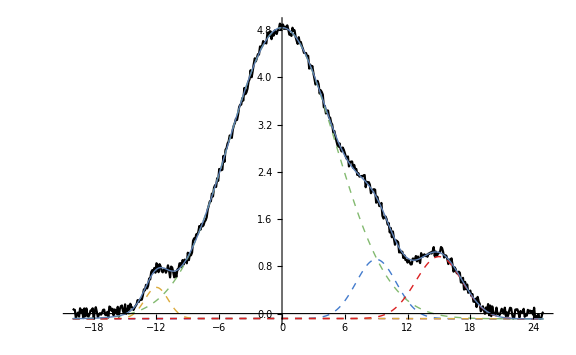
{1.00217 ⅇ^(-0.134569 (-9+x)^2),4.92363 ⅇ^(-0.0192921 x^2),0.528108 ⅇ^(-0.397016 (12+x)^2),1.05007 ⅇ^(-0.102341 (-15+x)^2)}
-Graphics-

```mathematica
PeakSplit[data,{9,0,-12,15},100]
```

```mathematica
BackgroundModulation[data]
```